# An Introduction to Spectral Graph Theory

I verify the bipartite graph theorem on a large graph then provide an example of the spectral graph theorem can be used.

James Pedersen, Jun. 24,  2018

According to theorems 4 and 6 in:

```mathematica
Hyperlink[https://people.orie.cornell.edu/dpw/orie6334/lecture3.pdf]
```

, If G is a connected undirected graph G with adjacency matrix A and λ_1≤ ... ≤ λ_n are the eigenvalues of A, G is bipartite iff λ_n=-λ_1.

## Examples:

Consider the graph

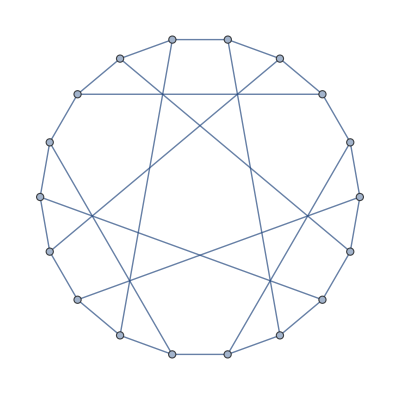

```mathematica
g=GraphData["PappusGraph"]
```

g is a connected graph:

```mathematica
ConnectedGraphQ[g]
```

True

Sorting the eigenvalues of g in ascending order,

```mathematica
Sort[Eigenvalues[AdjacencyMatrix[g]],Less]
```

{-3,-√3,-√3,-√3,-√3,-√3,-√3,0,0,0,0,√3,√3,√3,√3,√3,√3,3}

we see that -(-3) = 3, so g must be bipartite.

```mathematica
BipartiteGraphQ[g]
```

True

In fact, Mathematica’s graph embedding tools make it easy to for one to see that g is bipartite:

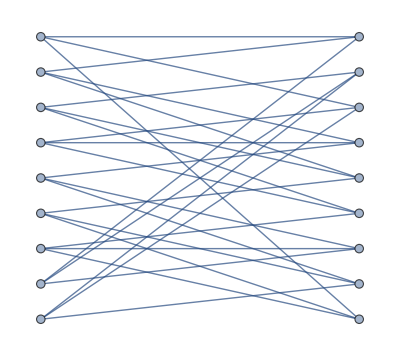

```mathematica
Graph[VertexList[g],EdgeList[g],GraphLayout->"BipartiteEmbedding"]
```

What about a negative example? Consider the following graph:

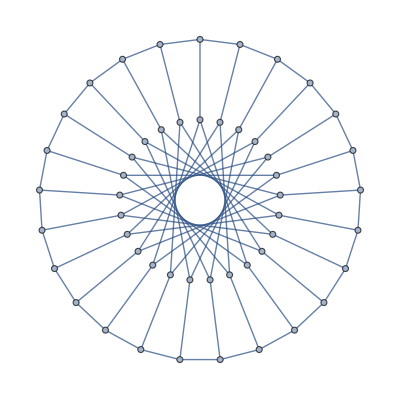

```mathematica
g=PetersenGraph[25,15]
```

```mathematica
Sort[N[Eigenvalues[AdjacencyMatrix[g]]], Less]
```

{-2.74606,-2.74606,-2.46106,-2.46106,-2.32412,-2.32412,-2.07289,-2.07289,-1.94908,-1.94908,-1.88001,-1.88001,-1.87603,-1.87603,-1.3577,-1.3577,-0.994792,-0.994792,-0.731528,-0.731528,-0.431826,-0.431826,-0.0466154,-0.0466154,0.0356204,0.0356204,0.0935099,0.0935099,0.580442,0.580442,0.957921,0.957921,1.,1.12418,1.12418,1.23806,1.23806,1.4027,1.4027,2.12259,2.12259,2.19914,2.19914,2.258,2.258,2.33503,2.33503,2.52452,2.52452,3.}

Here -2.74606 is not equal to -3, so g cannot be bipartite.

```mathematica
BipartiteGraphQ[g]
```

False

note that attempting to visualize g as a bipartite graph fails, as expected:

```mathematica
Graph[VertexList[g],EdgeList[g],GraphLayout->"BipartiteEmbedding"]
```

One more large example, creating a large connected undirected graph directly from an adjacency matrix:

```mathematica
A=Table[Table[RandomInteger[1],{k,n}],{n,49}]
B=Reverse[Reverse/@A]
adjmatrix=Thread[Join[{A,B}]];
g=AdjacencyGraph[adjmatrix]
```

{{0},{0,0},{1,0,1},{0,0,1,0},{0,1,1,0,0},{0,1,1,0,0,1},{1,0,1,1,0,1,0},{0,1,0,1,0,0,0,0},{1,1,0,0,1,1,0,0,1},{1,0,1,1,1,0,1,1,1,1},{1,1,1,1,0,0,0,0,1,0,1},{1,0,0,0,0,0,1,1,1,1,1,1},{0,0,0,1,0,1,0,1,1,1,0,0,0},{1,1,0,1,0,0,0,0,1,0,1,0,1,1},{0,1,1,0,1,0,0,1,0,1,1,1,1,1,1},{0,1,0,1,0,0,0,1,0,0,0,1,0,0,1,1},{1,1,1,0,1,0,0,1,0,0,0,1,1,0,1,0,1},{1,1,1,1,1,0,1,1,0,1,0,1,0,0,0,1,0,1},{0,1,0,1,1,0,0,1,1,1,0,1,1,0,1,0,1,0,1},{0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,0,0},{1,0,0,0,1,0,1,1,0,1,1,0,0,0,1,1,0,0,0,1,1},{0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1,0,1},{0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0},{1,1,0,1,0,0,0,1,0,0,1,1,0,1,1,1,1,1,1,0,0,1,0,0},{1,1,1,0,1,0,0,1,1,0,1,1,0,0,1,0,1,1,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,0,1,1,1,1,0,0,1,0,1,0,0,0,1,0,0,0,1,1},{0,0,0,0,0,1,0,0,1,0,1,1,1,1,0,1,0,0,1,0,1,0,0,1,0,0,1},{1,0,1,0,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0,1,0,1,0,0,0,0,1},{0,1,0,0,1,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,1,1},{1,1,0,1,0,0,0,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1},{0,0,1,1,1,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,0,0,1,1,1,1,0,1,1,0,0},{1,0,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,1,0,0,0,1,1,0,1,0,1,1,0,0},{0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1,0,1,0,1,0,1,0,0,1},{1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,1,1,0,1,1,0,1,0,0,1},{0,0,0,1,0,0,1,1,0,1,1,0,0,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,0,1,1,0,0,1,1},{1,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,1,1,1,1,1,0,1,1,1,1,1,0,0,1,1,1,0,0,0,1},{0,1,0,1,0,0,0,0,0,1,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,1,1,0,1,0,0},{1,1,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,0,1,1,1,0,0,0},{0,0,1,1,0,1,0,0,1,0,1,1,0,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1,1,0,1,1,1,1,1,0,0,0,0},{1,0,1,0,0,1,0,0,1,1,1,1,0,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,1,1,0,1,1,1,1},{1,1,0,0,0,1,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,0,1,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,0},{0,1,1,1,1,1,0,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,1,1,1,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0},{1,0,0,0,1,1,1,0,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,1,1,1,0,1,0},{1,1,1,1,0,0,1,0,0,1,1,0,1,1,1,0,1,0,0,0,0,1,1,1,0,0,1,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,0,0,1},{0,1,1,0,0,1,1,1,1,1,0,1,0,0,0,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,0,0,1,0,0,1,0,1,0,0,0},{1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,1,0,0,0,1},{1,1,1,1,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,1,0,1,1,0,1,1,1,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,0,0,0,0},{1,1,0,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,1,0,1,0,1,0,1,0,0,0,0}}

{{0,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,1,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,1},{0,0,0,0,0,1,0,0,0,1,1,0,1,1,0,1,1,0,0,1,1,1,0,1,1,0,1,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,1,1,1,1},{1,0,0,0,1,1,1,0,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,1,1,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1,0,1,1,1,0,1,1},{0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,0,0,0,1,0,1,1,1,1,1,0,0,1,1,0},{1,0,0,1,1,0,1,1,0,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,0,0,0,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1,1,1,1},{0,1,0,1,1,1,1,1,1,0,1,0,0,0,1,0,1,1,1,0,1,0,1,1,0,0,1,1,0,1,0,1,1,0,0,1,0,1,1,1,0,0,0,1},{0,0,0,0,1,1,0,0,0,0,1,0,0,1,0,0,0,1,1,1,1,1,1,0,0,1,0,0,1,0,1,0,1,0,1,0,0,1,1,1,1,1,0},{0,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,1,1,0,0,1},{1,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,1,0,0,1,0,1,0,1,1,1,0,1,1,1,0,0,1,1,1,1,0,0,0,1,1},{1,1,1,1,0,1,1,1,0,0,1,1,0,0,0,0,1,1,1,0,0,0,1,1,0,0,0,0,1,1,1,1,0,0,1,0,0,1,0,1},{0,0,0,0,1,1,1,1,1,0,1,1,1,0,1,1,0,0,1,1,0,0,0,1,1,1,0,1,1,0,1,0,0,1,0,1,1,0,0},{0,0,0,1,1,1,0,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,1,1,1,0,0,0,1,1,1,0,0,0,0,0,1,1},{0,0,1,0,1,1,0,1,0,1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1,0,1,1,0,0,0,0,0,1,0,1,0},{1,0,0,0,1,1,1,0,0,1,1,1,1,1,0,1,1,1,1,1,0,0,1,0,0,0,1,0,1,0,0,0,1,0,1,1},{1,1,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,1,1,0,0,1,0,0,1,1,0,1,1,0,0,1,0,0,0},{1,0,0,1,0,1,1,0,1,1,0,0,1,0,0,1,1,0,0,0,0,1,1,1,0,1,0,0,1,1,1,1,0,1},{1,0,0,1,0,1,0,1,0,1,1,0,1,1,0,0,0,0,1,1,1,1,1,0,1,1,0,1,1,0,1,1,0},{0,0,1,1,0,1,0,1,1,0,0,0,1,0,1,0,0,1,1,0,0,0,1,1,0,0,0,1,0,0,0,1},{0,0,1,1,0,1,1,1,1,0,0,1,1,0,0,1,1,1,0,0,1,0,0,0,0,0,1,1,1,0,0},{1,1,0,0,1,1,0,0,0,0,1,0,1,0,0,1,0,1,0,0,0,1,1,0,0,0,1,0,1,1},{1,1,0,0,0,0,1,1,0,1,0,1,0,1,1,0,0,1,0,1,0,1,0,0,1,0,0,1,0},{1,0,0,0,0,1,0,1,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0,0,1,0,1},{1,0,0,1,0,0,1,0,1,0,0,1,0,1,1,1,1,0,1,0,0,1,0,0,0,0,0},{1,1,0,0,0,1,0,0,0,1,0,1,0,0,1,1,1,1,0,0,0,0,0,0,1,0},{1,0,0,0,0,1,0,1,1,0,1,0,0,1,1,0,1,1,0,0,1,0,1,1,1},{0,0,1,0,0,1,1,1,1,1,1,0,1,1,0,0,1,0,0,0,1,0,1,1},{0,0,0,1,0,0,1,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0},{1,0,1,0,0,1,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,0},{1,1,0,0,0,1,1,0,0,0,1,1,0,1,1,0,1,0,0,0,1},{0,0,0,1,0,1,1,1,1,1,0,1,1,1,1,0,1,0,1,0},{1,0,1,0,1,0,1,1,0,1,1,1,0,0,1,1,0,1,0},{1,0,1,0,0,0,1,0,1,0,1,1,0,1,1,1,1,1},{1,0,1,0,1,1,0,0,0,1,0,0,1,0,1,1,1},{1,1,0,0,1,0,0,0,1,0,0,0,1,0,1,0},{1,1,1,1,1,1,0,1,0,0,1,0,1,1,0},{1,1,0,1,0,1,0,0,0,0,1,0,1,1},{0,0,0,1,1,1,0,1,0,1,0,0,0},{1,1,1,1,1,1,0,0,0,0,0,1},{1,0,1,0,0,0,0,1,1,1,1},{1,1,1,1,0,1,1,1,0,1},{1,0,0,1,1,0,0,1,1},{0,0,0,0,1,0,1,0},{0,1,0,1,1,0,1},{1,0,0,1,1,0},{0,0,1,1,0},{0,1,0,0},{1,0,1},{0,0},{0}}

AdjacencyGraph[{{0},{0,0},{1,0,1},{0,0,1,0},{0,1,1,0,0},{0,1,1,0,0,1},{1,0,1,1,0,1,0},{0,1,0,1,0,0,0,0},{1,1,0,0,1,1,0,0,1},{1,0,1,1,1,0,1,1,1,1},{1,1,1,1,0,0,0,0,1,0,1},{1,0,0,0,0,0,1,1,1,1,1,1},{0,0,0,1,0,1,0,1,1,1,0,0,0},{1,1,0,1,0,0,0,0,1,0,1,0,1,1},{0,1,1,0,1,0,0,1,0,1,1,1,1,1,1},{0,1,0,1,0,0,0,1,0,0,0,1,0,0,1,1},{1,1,1,0,1,0,0,1,0,0,0,1,1,0,1,0,1},{1,1,1,1,1,0,1,1,0,1,0,1,0,0,0,1,0,1},{0,1,0,1,1,0,0,1,1,1,0,1,1,0,1,0,1,0,1},{0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,0,0},{1,0,0,0,1,0,1,1,0,1,1,0,0,0,1,1,0,0,0,1,1},{0,0,0,0,1,0,1,0,0,0,0,1,1,1,0,1,1,0,0,1,0,1},{0,0,0,0,1,1,0,1,1,0,0,0,0,1,0,0,1,0,0,1,0,0,0},{1,1,0,1,0,0,0,1,0,0,1,1,0,1,1,1,1,1,1,0,0,1,0,0},{1,1,1,0,1,0,0,1,1,0,1,1,0,0,1,0,1,1,0,1,0,0,0,0,1},{0,1,0,0,0,0,0,0,1,1,1,1,0,0,1,0,1,0,0,0,1,0,0,0,1,1},{0,0,0,0,0,1,0,0,1,0,1,1,1,1,0,1,0,0,1,0,1,0,0,1,0,0,1},{1,0,1,0,0,0,1,0,1,0,1,1,1,1,0,1,0,1,0,0,1,0,1,0,0,0,0,1},{0,1,0,0,1,0,0,1,0,1,0,1,0,0,1,1,0,1,0,1,0,1,1,0,0,0,0,1,1},{1,1,0,1,0,0,0,1,1,0,0,0,1,0,1,0,0,1,0,1,0,0,0,0,1,1,0,0,1,1},{0,0,1,1,1,0,0,0,0,0,1,0,0,1,1,1,0,0,1,1,0,0,1,1,1,1,0,1,1,0,0},{1,0,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,1,0,0,0,1,1,0,1,0,1,1,0,0},{0,1,1,0,1,1,0,1,1,0,1,1,1,1,1,0,0,0,0,1,1,0,1,1,0,1,0,1,0,1,0,0,1},{1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,0,0,1,1,0,0,1,0,0,1,1,0,1,1,0,1,0,0,1},{0,0,0,1,0,0,1,1,0,1,1,0,0,1,0,0,1,1,0,1,0,0,0,1,1,0,1,1,0,1,1,0,0,1,1},{1,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,1,1,1,1,1,0,1,1,1,1,1,0,0,1,1,1,0,0,0,1},{0,1,0,1,0,0,0,0,0,1,1,0,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,1,1,0,1,0,0},{1,1,0,0,0,0,0,1,1,1,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,0,1,0,1,0,0,0,1,1,1,0,0,0},{0,0,1,1,0,1,0,0,1,0,1,1,0,1,1,1,0,0,0,1,1,0,0,1,1,0,1,1,1,0,1,1,1,1,1,0,0,0,0},{1,0,1,0,0,1,0,0,1,1,1,1,0,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,1,1,0,0,1,1,1,0,1,1,1,1},{1,1,0,0,0,1,1,1,1,0,0,1,1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,1},{1,0,0,1,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,0,0},{0,1,1,1,1,1,0,0,1,0,1,0,1,0,1,0,0,1,0,0,1,1,1,1,1,1,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0},{1,0,0,0,1,1,1,0,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,1,1,1,1,1,0,1,0},{1,1,1,1,0,0,1,0,0,1,1,0,1,1,1,0,1,0,0,0,0,1,1,1,0,0,1,0,1,1,1,0,0,0,0,1,0,1,1,0,1,1,0,0,1},{0,1,1,0,0,1,1,1,1,1,0,1,0,0,0,1,0,0,1,1,0,1,0,1,1,0,0,1,1,0,1,0,1,0,0,0,0,1,0,0,1,0,1,0,0,0},{1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,0,1,1,0,1,0,1,0,0,1,0,0,1,0,0,1,0,0,0,1,1,1,0,0,0,1},{1,1,1,1,0,1,1,1,1,1,1,0,0,0,1,1,1,1,1,1,0,1,0,1,1,0,1,1,1,0,0,1,1,0,1,1,0,1,1,0,0,0,1,0,0,0,0,0},{1,1,0,0,1,0,0,1,0,1,0,1,1,0,1,0,1,0,0,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,1,0,1,0,1,0,1,0,0,0,0}},SparseArray[…]]

```mathematica
Transpose[A]
```

Transpose[{{0},{0,1},{1,0,0},{0,1,0,0},{1,0,0,1,1},{0,0,1,1,1,1},{1,1,0,1,1,1,0},{1,1,0,0,1,0,0,0},{0,1,0,1,0,1,0,0,1},{0,0,1,1,1,1,0,1,1,1},{0,0,0,1,1,1,1,0,1,0,0},{0,0,0,1,1,1,0,1,1,0,0,1},{1,1,1,1,0,1,1,1,0,1,0,1,1},{0,0,0,1,0,1,0,1,0,1,1,0,1,0},{0,0,1,1,0,0,0,1,0,0,1,0,0,1,1},{0,1,0,0,0,1,0,0,0,0,0,0,1,1,1,0},{0,1,0,0,1,0,1,0,1,0,1,1,1,0,0,1,0},{0,0,1,0,1,1,1,0,1,0,1,1,1,1,1,0,1,1},{1,1,0,0,1,0,0,0,1,1,1,1,1,0,0,1,1,0,0},{0,1,1,0,1,1,0,0,1,1,0,0,1,1,1,0,1,0,0,1},{1,0,0,0,1,1,0,1,1,1,1,1,1,1,1,1,1,0,0,1,0},{0,0,1,1,0,1,0,1,0,0,1,0,0,1,1,1,0,0,1,0,0,0},{1,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,1,1,1,1},{0,1,0,0,0,1,0,0,0,0,1,1,0,1,0,0,1,1,1,1,0,0,1,1},{1,0,1,0,0,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,0,1,1},{0,0,1,1,1,1,1,1,0,1,0,1,0,1,0,1,0,1,1,0,1,1,0,1,1,0},{0,0,1,1,1,0,1,1,1,1,0,1,0,0,0,0,0,1,1,0,0,1,0,0,1,0,1},{1,0,1,1,1,1,0,0,0,0,1,1,1,0,0,1,0,1,1,1,1,1,0,1,0,0,1,0},{1,1,1,1,1,1,0,0,1,0,0,0,1,1,1,1,1,1,1,0,0,0,0,1,0,1,1,0,0},{0,0,0,0,1,1,0,1,1,1,1,1,0,0,0,0,1,0,1,0,1,1,1,1,0,0,0,1,1,0},{0,0,1,0,1,0,0,1,1,0,1,0,1,1,1,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0},{0,0,0,1,0,1,1,1,1,0,0,1,0,0,1,1,1,0,1,1,0,0,0,0,1,1,1,0,1,0,0,1},{1,0,0,0,0,1,0,0,1,0,0,0,1,0,1,1,0,0,1,1,0,0,0,1,1,1,0,0,1,0,0,0,1},{0,1,0,1,1,1,1,0,1,0,0,1,1,0,0,0,1,0,1,1,1,0,1,0,0,1,1,0,0,1,0,0,0,1},{0,0,1,1,1,0,1,0,0,0,1,0,1,0,1,0,1,1,0,1,0,1,0,1,0,1,0,0,1,1,1,0,0,0,0},{1,0,0,1,0,0,1,0,0,1,0,0,1,0,1,0,1,1,0,1,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0},{1,0,1,0,0,0,1,1,1,1,1,1,0,0,0,1,1,1,0,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,1,1,0,0,0,1,0,0,1,0,1,1,0,0,1,0,1,1,1,1,1,0,1,0,0,1,1,1,0,0,0,1,1,0,0},{1,0,1,1,1,0,1,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{1,1,0,1,1,1,1,0,1,1,0,0,0,1,0,0,0,1,1,1,0,0,0,0,1,1,0,1,0,1,1,0,1,0,1,1,0,1,0,0},{0,1,0,0,0,0,0,1,1,0,0,0,0,0,1,1,1,1,0,0,0,0,0,1,1,1,1,0,1,1,1,1,1,0,0,1,0,0,0,1,0},{1,0,0,1,1,0,1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,0,0,1,0,0,1,1,0,1,1,0,1,0,0,1,0,1,0,0,1,0},{1,1,1,1,0,1,0,1,0,0,1,1,0,0,0,0,1,0,1,1,0,1,0,0,0,1,0,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0,1,0,1,1,0,1,0,0,0,0,1,1,0,1,1,0,1,0,0,1,0,1,0,0,1,0},{1,1,1,1,1,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,0,0,1,1,1,1,0,1,0,0,1,0,0,1,0,1,1,1,1,1,1,0,0,0},{0,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,1,1,0,0,1,1,1,1,1,0,0,0,1,1,0,1,0,1,1,0,0,0,0,0,0,1,0,0,0,0},{1,0,0,1,1,0,0,0,0,1,0,0,1,0,1,1,0,0,0,1,1,1,1,1,1,0,0,1,1,1,0,1,1,0,1,0,0,1,0,0,0,1,0,0,0,0,0},{0,1,1,1,1,1,1,1,1,1,1,0,1,0,1,0,0,1,1,0,0,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,0,0,0,1,0,1,1,0,0,1,1,0},{0,0,0,0,1,1,0,1,1,1,1,1,1,0,0,1,1,0,1,1,0,0,0,0,0,1,0,0,1,0,0,1,1,1,0,1,1,1,0,1,0,1,0,0,1,1,1,0,1}}]

## Section Header

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)

```mathematica
GraphData["Hadamard",{"24","9"}]
```

GraphData[Hadamard,{24,9}]

```mathematica
GraphData[{"CrossedPrism",5}]
```

GraphData[{CrossedPrism,5}]